```mathematica
description="El Ael -> Mu Amu, QED, total cross section, tree";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
```

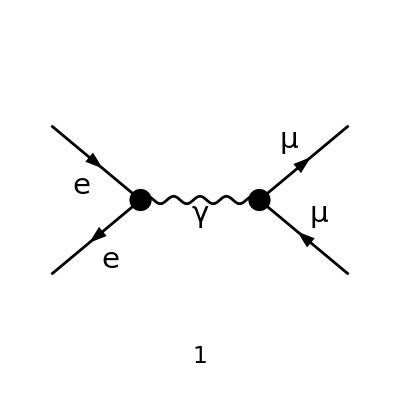

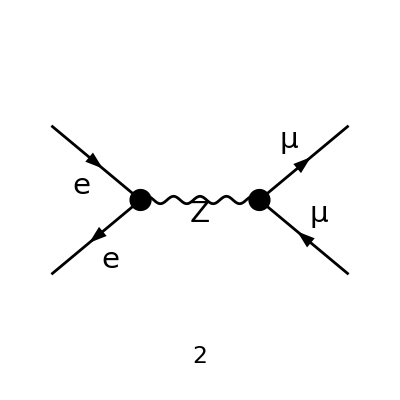

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes}];

Paint[DiagramExtract[diags,3..4],ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags,4..4]],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True]

ampE[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags,3..3]],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True]
```

1/((OverBar[k_1]+OverBar[k_2])^2-m_Z^2)(φ(-OverBar[p_2],m_e)).((ⅈ e (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(ⅈ e (γ̄)^Lor1.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1],m_e)) (φ(OverBar[k_1],m_μ)).((ⅈ e (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(ⅈ e (γ̄)^Lor1.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(-OverBar[k_2],m_μ))

-(e^2 (φ(-OverBar[p_2],m_e)).(γ̄)^Lor1.(φ(OverBar[p_1],m_e)) (φ(OverBar[k_1],m_μ)).(γ̄)^Lor1.(φ(-OverBar[k_2],m_μ)))/(OverBar[k_1]+OverBar[k_2])^2

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_e"],SMP["m_e"],SMP["m_mu"],SMP["m_mu"]];
```

```mathematica
ampSquared[0]=(amp[0] (ComplexConjugate[ampE[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//Simplify
```

(e^4 (m_e^2 (2 m_μ^2 (1-4 (sin(θ_W))^2)^2+16 (s-t-u) (sin(θ_W))^4+8 (-s+t+u) (sin(θ_W))^2+s-2 u)+m_e^4 (1-4 (sin(θ_W))^2)^2+m_μ^2 (16 (s-t-u) (sin(θ_W))^4+8 (-s+t+u) (sin(θ_W))^2+s-2 u)+m_μ^4 (1-4 (sin(θ_W))^2)^2+8 t^2 (sin(θ_W))^4-4 t^2 (sin(θ_W))^2+8 u^2 (sin(θ_W))^4-4 u^2 (sin(θ_W))^2+u^2))/(4 s (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2)

```mathematica
FinalSubstitutions={SMP["m_e"]->0,SMP["m_mu"]->0};

ampSimp = ampSquared[0]/.FinalSubstitutions/.{u->(-s-t)}//Simplify
```

(e^4 (8 (s^2+2 s t+2 t^2) (sin(θ_W))^4-4 (s^2+2 s t+2 t^2) (sin(θ_W))^2+(s+t)^2))/(4 s (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2)